```mathematica
(*ML Data*)

(*differences Y Vector*)
Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLaccuracy.xlsx"];
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

20

```mathematica
(*the whole Y Vec*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

20

```mathematica
(*fitting to 90% of the data*)
n90=Floor[nΔYVec (0.9)]
```

18

```mathematica
(*Covariates*)

(*Accuracy Energy*)
X1Vec=Data[[1,All,3]];
(*X3Vec=X3Vec^2;*)

(*Accuracy COOL*)
X2Vec=Data[[1,All,4]];

(*Energy Unknowns*)
X3Vec=Data[[1,All,5]];

(*COOL Unknowns*)
X4Vec=Data[[1,All,6]];
```

```mathematica
(*Plot Y - Observed data*)
```

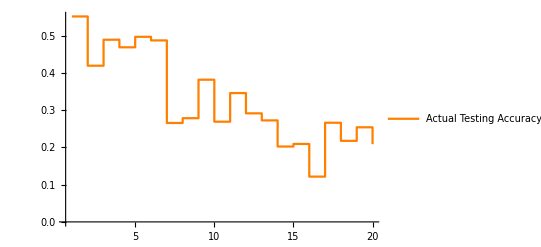

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->0, Joined->True,PlotRange->All,PlotStyle->Orange,PlotLegends->{"Actual Testing Accuracy"}]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=3)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]))/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];



Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];



Dβ12=Simplify[D[LnL,β12]];





Dβ21=Simplify[D[LnL,β21]];
Dβ22=Simplify[D[LnL,β22]];
Dβ23=Simplify[D[LnL,β23]];
Dβ24=Simplify[D[LnL,β24]];



Dβ28=Simplify[D[LnL,β28]];
Dβ29=Simplify[D[LnL,β29]];
Dβ30=Simplify[D[LnL,β30]];
Dβ31=Simplify[D[LnL,β31]];



Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ7},{0==Dβ8},{0==Dβ12},{0==Dβ21},{0==Dβ22},{0==Dβ23},{0==Dβ24},{0==Dβ28},{0==Dβ29},{0==Dβ30},{0==Dβ31},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β7,0.1},{β8,0.1},{β12,0.1},{β21,0.1},{β22,0.1},{β23,0.1},{β24,0.1},{β28,0.1},{β29,0.1},{β30,0.1},{β31,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦3⟧ is longer than depth of object.

Part::partd: Part specification X2⟦3⟧ is longer than depth of object.

Part::partd: Part specification X3⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→2.1808,β1→-3.66596,β2→-3.6161,β3→-0.121691,β7→9.07958,β8→0.0210896,β12→0.300731,β21→-1.59039,β22→0.376496,β23→-0.219121,β24→-0.0946106,β28→-0.435565,β29→-0.0263307,β30→0.41119,β31→0.0179347,σ→6.70397×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β12 X2[[i]] X3[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]] +β28 YVec[[i-2]] +β29 X1[[i-2]]+β30 X2[[i-2]]+β31 X3[[i-2]]/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec};
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]],ΔYVec[[2]]};
For[k=3,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X1Vec,X2-> X2Vec,X3->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression -2+i cannot be used as a part specification.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{0.,-0.132357,0.0701488,-0.0205767,0.0296938,-0.0114036,-0.220798,0.0120851,0.103672,-0.112688,0.0777192,-0.0551083,-0.0201579,-0.0706585,0.00662708,-0.0871632,0.145139,-0.0484086,0.0854969,-0.00408179}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.552,0.419643,0.489792,0.469215,0.498909,0.487505,0.266707,0.278792,0.382464,0.269777,0.347496,0.292387,0.27223,0.201571,0.208198,0.121035,0.266174,0.217765,0.303262,0.29918}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.552},{2,0.419643},{3,0.489792},{4,0.469215},{5,0.498909},{6,0.487505},{7,0.266707},{8,0.278792},{9,0.382464},{10,0.269777},{11,0.347496},{12,0.292387},{13,0.27223},{14,0.201571},{15,0.208198},{16,0.121035},{17,0.266174},{18,0.217765},{19,0.303262},{20,0.29918}}

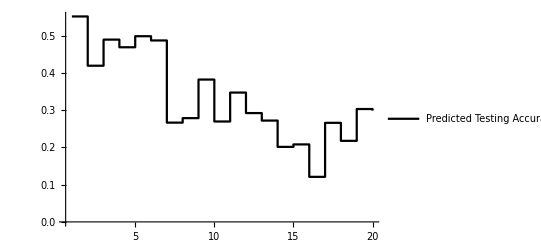

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->0, Joined->True,PlotStyle->Black,PlotRange->All,PlotLegends->{"Predicted Testing Accuracy"}]
```

Show::gcomb: Could not combine the graphics objects in ….

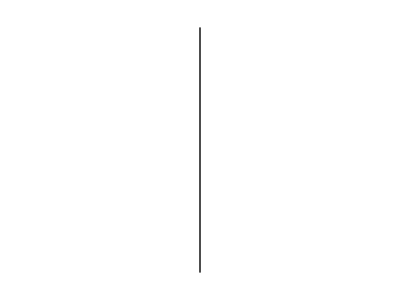
Show[{-Graphics-,-Graphics-},-Graphics-,PlotRange→All]

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)


A=Show[{YObserved,YPredictedPlotInt},Graphics[{Black, Line[{{n90,0},{n90,1}}]}],PlotRange->All]
```

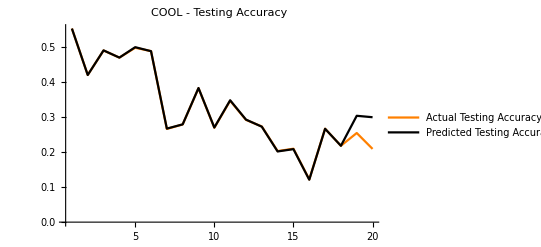

```mathematica
A=ListPlot[{dataPlot,NewPlot},InterpolationOrder->1, Joined->True,PlotStyle->{Orange,Black},PlotRange->All,PlotLegends->{"Actual Testing Accuracy","Predicted Testing Accuracy"},PlotLabel->"COOL - Testing Accuracy"]
```

```mathematica
B=Graphics[{Black, Dashed,Line[{{n90,0},{n90,1}}]}];
```

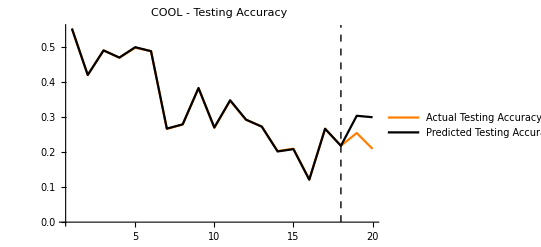

```mathematica
Show[A,B]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0105804

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.0105712

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.00352372

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->6
```

0.888949